```mathematica
(*Harmonic oscillator Schrodinger solution - http://mathematica.stackexchange.com/questions/32293/find-eigen-energies-of-time-independent-schr%C3%B6dinger-equation *)
```

```mathematica
xOp[dim_]:=SparseArray[{Band[{1,2}]->#,Band[{2,1}]->#},{#,#}&@dim]&[Table[Sqrt[i],{i,dim-1}]/Sqrt[2]]

eKin[dim_]:=1/2 SparseArray[{Band[{1,1}]->Table[i-1/2,{i,dim}],Band[{1,3}]->#,Band[{3,1}]->#},{#,#}&@dim]&[Table[-Sqrt[i (i+1)/2],{i,dim-2}]/Sqrt[2]]
```

```mathematica
spectrum[n_,tolerance_: .00001][potential_,var_]/;PolynomialQ[potential,var]:=Module[{x,h,e,v,c=CoefficientList[potential,var],min=First@Check[Minimize[potential,var],Print["No absolute potential minimum found. Make sure the leading power has a positive coefficient!"];
Abort[],Minimize::natt]},FixedPoint[{#[[1]]+1,Eigenvalues[h=eKin[#[[1]]]+N[Sum[c[[i]] MatrixPower[xOp[#[[1]]],i-1],{i,2,Length[c]}]+(c[[1]]-min) IdentityMatrix[#[[1]]]],-n]}&,{n+1,2 Reverse@Range[n]-1},SameTest->(Max@Abs[#1[[2]]-#2[[2]]]<tolerance&)];
{e,v}=Reverse/@Eigensystem[h,-n]
{e+min,ψe/@v}]
```

```mathematica
Format[ψe[l_List]]:=ψe[Row[{"«",Length[l],"»"}]]
ψe[l_List][x_]:=1/(Pi^(1/4))Exp[-x^2/2] l.(1/Sqrt[2^# #!] HermiteH[#,x]&[Range[Length[l]]-1])

plotSpectrum[data_,potential_,{var_,min_,max_}]:=Show[Apply[Plot[Evaluate[#1+(Last[#1]-First[#1])/(2+Length[#1])/2 Through[#2[var]]],{var,min,max},Prolog->{Gray,Map[Line[{{min,#},{max,#}}]&,#1]},Frame->True]&,data],Plot[potential,{var,min,max}]]
```

```mathematica
spectrum[10][1/2 x^2,x]
```

{{0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5,8.5,9.5},{ψe[«15»],ψe[«15»],ψe[«15»],ψe[«15»],ψe[«15»],ψe[«15»],ψe[«15»],ψe[«15»],ψe[«15»],ψe[«15»]}}

```mathematica
(*Mexican hat anharmonic oscillator Schrodinger solution - http://mathematica.stackexchange.com/questions/32293/find-eigen-energies-of-time-independent-schr%C3%B6dinger-equation *)
```

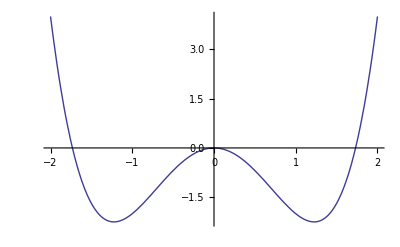

```mathematica
Plot[-3 x^2+x^4,{x,-2,2}]
```

```mathematica
ψ1=spectrum[5][-10 x^2+x^4,x]//Last//Last
```

ψe[«72»]

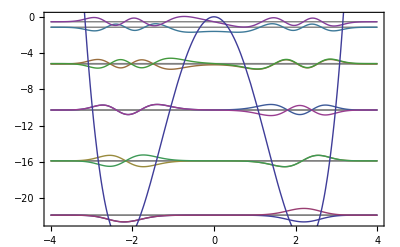

```mathematica
With[{v=-10 x^2+x^4,n=10},plotSpectrum[spectrum[n][v,x],v,{x,-4,4}]]
```

```mathematica
First[spectrum[100][1/2 x^2,x]]
```

{0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5,8.5,9.5,10.5,11.5,12.5,13.5,14.5,15.5,16.5,17.5,18.5,19.5,20.5,21.5,22.5,23.5,24.5,25.5,26.5,27.5,28.5,29.5,30.5,31.5,32.5,33.5,34.5,35.5,36.5,37.5,38.5,39.5,40.5,41.5,42.5,43.5,44.5,45.5,46.5,47.5,48.5,49.5,50.5,51.5,52.5,53.5,54.5,55.5,56.5,57.5,58.5,59.5,60.5,61.5,62.5,63.5,64.5,65.5,66.5,67.5,68.5,69.5,70.5,71.5,72.5,73.5,74.5,75.5,76.5,77.5,78.5,79.5,80.5,81.5,82.5,83.5,84.5,85.5,86.5,87.5,88.5,89.5,90.5,91.5,92.5,93.5,94.5,95.5,96.5,97.5,98.5,99.5}